```mathematica
Bezier curves
Definitions
```

```mathematica
Generic Bezier curve equation (of n-th order) with n control points pts.
```

```mathematica
Bez [t_,pts_] := Module[ 
{n = Length[pts]-1},
Sum[ Binomial[n,i](1-t)^(n-i)If[i ==0 And t ==0, 1,t^i]pts[[i+1]], {i,0,n}]
]
```

```mathematica
Parametric plot of a Bezier curve showing the curve and the control points :
```

```mathematica
PlotBezier[pts_] :=Show[ParametricPlot[Bez[t,pts],{t,0,1}, PlotStyle ->{Thick,Blue}], ListLinePlot[pts, PlotStyle -> {Red,Dashed}, PlotMarkers->"●"], PlotRange->All, AxesOrigin->{0,0}]
```

```mathematica
Find the t's that are solution for the given point p on the Bezier curve defined by the control points pts.
If the point p is not part of the curve, the resulting list will be empty.
```

```mathematica
SolveBezierT[p_,pts_] :=Solve[p ==  Bez[t,pts],t]
```

```mathematica
Examples
```

```mathematica
pts := {{100,500},{25,400},{475,400},{400,500}}
```

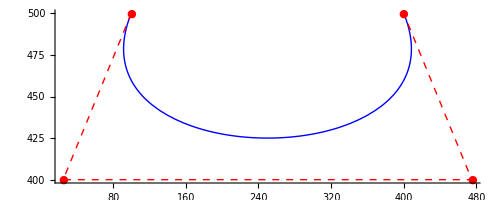

```mathematica
PlotBezier[pts]
```

```mathematica
SolveBezierT[{100,500},pts]
```

{{t→0}}

```mathematica
cubicBezier = {{x1,y1},{x2,y2},{x3,y3}}
```

{{x1,y1},{x2,y2},{x3,y3}}

```mathematica
Bez[t, cubicBezier]
```

{(1-t)^2 x1+2 (1-t) t x2+t^2 x3,(1-t)^2 y1+2 (1-t) t y2+t^2 y3}